```mathematica
Remove["Global`*"]
```

```mathematica
(*thkim*)
```

## 1 Get eigen

## 1.1 Setup

```mathematica
m={m0,m0,m1};
wmhz=2*Pi*1*^6;Num =Length[m];
kM =Append[ Array[k,{2,2}],{kz,kz}];kM=Transpose[Table[If[m[[i]]===m0,kM[[1;;,1]],kM[[1;;,2]]],{i,Num}]];
xM = Array[x,{3,Num}];
(*Calculate equilibrium positions (axial crystal)*)
z0M = Array[z0,Num];
L0EQ [i_]:=z0M[[i]]==(Sum[(z0M[[i]] - z0M[[k]])^(-2),{k,1,i-1}] - Sum[(z0M[[i]] - z0M[[k]])^(-2),{k, i+1,Num}])
L0EQlist =L0EQ/@Range[Num]//FullSimplify;
guessz0=Range[-#,#,2*#/(Num-1)]&[0.7*Num^(2/3)];pos=Transpose[Append[{z0M},guessz0]];z0M=z0M/.Chop[FindRoot[L0EQlist,pos]];
L0Mn[i_,j_,n_]:=If[i==j,0,Abs[z0M[[i]]-z0M[[j]]]^n]
(*Create matrix*)
ke2=2.306569*^-28;l0=(ke2/kz)^(1/3);
ics=ArrayReshape[Append[Table[xM[[d,i]]->0,{d,2},{i,Num}],Table[(xM[[3,i]]-xM[[3,j]])->L0Mn[i,j,1]*l0,{i,Num},{j,i+1,Num}]],{Num*(Num+3)/2}];
Uel=Total[0.5*kM*(xM^2),2]+ke2*Sum[(Total[(xM[[;;,i]]-xM[[;;,j]])^2])^(-0.5),{i,Num},{j,i+1,Num}];
Vel1=-Table[D[Uel,{xM[[d,i]]},{xM[[d,j]]}]/Sqrt[m[[i]]*m[[j]]],{d,3},{i,Num},{j,Num}]/.ics//FullSimplify;
Vel1norm=Vel1/.{m1->m0,k[1,2]->k[1,1],k[2,2]->k[2,1]}//FullSimplify;
(*Subbing in secular frequency expressions*)
{k[1,1],k[1,2]}=κr^2*3.25*^-40*V0^2/w^2/r0^4/{m0,m1}+1.602*^-13*(κr*V1/r0^2-κz*U/z0^2)//FullSimplify;
{k[2,1],k[2,2]}=κr^2*3.25*^-40*V0^2/w^2/r0^4/{m0,m1}+1.602*^-13*(-κr*V1/r0^2-κz*U/z0^2)//FullSimplify;
kz=3.204*^-13*κz*U/z0^2//FullSimplify;
```

```mathematica
(*monroe results*)
eq1=3.06*wmhz==Sqrt[(1.602*^-19*V0)^2*0.3/2/(2*^-4)^4/(w)^2/(171*1.66054*^-27)^2-1.602*^-19*U/(171*1.66054*^-27)/(z0)^2];
eq2=0.16*wmhz==Sqrt[2*1.602*^-19*U/(171*1.66054*^-27)/(4*^-4)^2];
```

## 1.2 Sub in Values

```mathematica
m0=38*1.66054*^-27;m1=45*1.66054*^-27;κr=1;κz=1;r0=0.2;z0=0.41278;V1=0;
```

```mathematica
U=1;V0=100.8;w=40.25;
```

```mathematica
Sqrt[k[1,1]/m0]/wmhz
```

2.77976

```mathematica
{th1,th2}=Eigensystem[Vel1[[1]]];th1=Sqrt[-th1]/wmhz;
th1//MatrixForm
th2//MatrixForm
```

(2.7378
2.49961
2.17032)

(0.802688 | 0.578646 | 0.144434
0.594169 | -0.754956 | -0.277497
0.0515314 | -0.308562 | 0.949807)

## 1.3 Get normal modes - Z

```mathematica
monroewmvalsz={0.57,0.48,0.387,0.279,0.158};
```

```mathematica
wmvalsz[Ud_,z0d_]:=Sqrt[-Eigenvalues[Vel1[[3]]/.{U->Ud,z0->z0d}](*,-Eigenvalues[Vel1[[3]]/.{V->Vd,w->wd}]*)]/wmhz
wmvalszminfunc[Vd_,wd_]:=Norm[wmvalsz[Vd,wd]-monroewmvalsz]
```

```mathematica
NMinimize[{wmvalszminfunc[U,z0],0.16*wmhz==Sqrt[2*1.602*^-19*U/(171*1.66054*^-27)/(4*^-4)^2],0<U<100,0.2≤z0≤1},{U,z0}]
```

{0.000632733,{U→0.143309,z0→0.41278}}

```mathematica
wmvalsz[0.095485,0.336938]
```

{0.570002,0.479657,0.38706,0.279527,0.157959}

```mathematica
Sqrt[2*1.602*^-19*U/(171*1.66054*^-27)/(z0)^2]/wmhz/.{z0->4.1278*^-4,U->0.143309}
```

0.155046

## 1.4 Get normal modes - R

```mathematica
monroewmvalsr=Reverse[{3.039,3.048,3.056,3.062,3.403}];
```

```mathematica
wmvalsr[Vd_,wd_]:=Sqrt[-Eigenvalues[Vel1[[1]]/.{V0->Vd,w->wd}]]/wmhz
wmvalsrminfunc[Vd_,wd_]:=Total[(wmvalsr[Vd,wd]-monroewmvalsr)^2]
```

```mathematica
NMinimize[{wmvalsrminfunc[V,w](*,3.06*wmhz==Sqrt[(1.602*^-19*V)^2*0.3/2/(2*^-4)^4/(28.25*wmhz)^2/(171*1.66054*^-27)^2-1.602*^-19*U/(171*1.66054*^-27)/(z0)^2]*),100<V<1000,10≤w≤40},{V,w}]
```

{0.108526,{V→411.341,w→34.8796}}

```mathematica
{wmvalsr[#1,#2],wmvalsrminfunc[#1,#2]}&[342.8,28.25]
```

{{3.79033,3.06229,3.05602,3.04793,3.03899},0.150025}

```mathematica
Sqrt[k[1,1]/m0]/wmhz
Sqrt[k[1,2]/m1]/wmhz
```

3.06338

3.7964

## 1.3 Find Monroe Results

1.92265×10^7==√(-587989.+(4.58183×10^25 V0^2)/w^2)

False

```mathematica
Sqrt[2*1.602*^-19*U/(138*1.66054*^-27)/(4*^-4)^2]/wmhz
```

0.145382

```mathematica
Solve[{eq1,eq2},{V0,U}]
```

{{V0→-3.52205×10^-6 w,U→0.143309},{V0→3.52205×10^-6 w,U→0.143309}}

## 4 Pretty Pictures

```mathematica
eigenholder=Table[Eigensystem[Vel1[[d]]],{d,3}];
wmlist=Sqrt[-eigenholder[[;;,1]]]/wmhz;vlist=eigenholder[[;;,2]];
```

```mathematica
wmlist
vlist[[1,1]]//MatrixForm
```

{{3.79033,3.06229,3.05602,3.04793,3.03899},{3.79033,3.06229,3.05602,3.04793,3.03899},{0.570002,0.479658,0.38706,0.279527,0.157959}}

(0.000130765 | 0.000330231 | 0.00105601 | 0.00677876 | 0.999976
-0.631283 | -0.547547 | -0.45094 | -0.31356 | 0.00286518
0.679219 | -0.0740721 | -0.475696 | -0.55396 | 0.00419324
0.357694 | -0.674504 | -0.12266 | 0.634065 | -0.00399277
0.110448 | -0.489643 | 0.745198 | -0.439005 | 0.00233627)

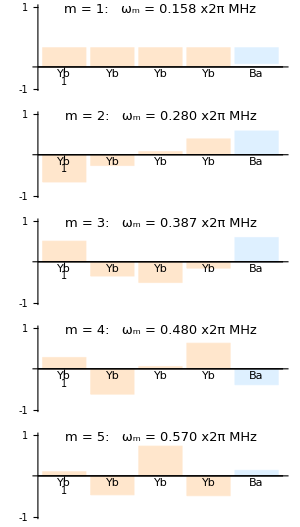
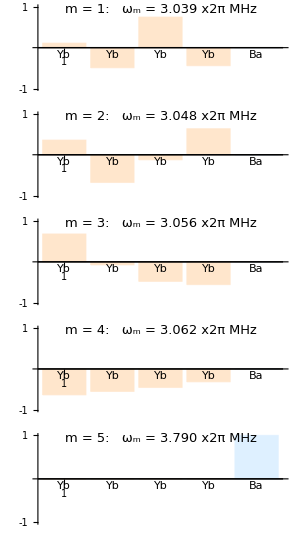

```mathematica
monroeplot=Table[BarChart[vlist[[#,i]],PlotRange->{-1,1},ChartStyle->{LightOrange,LightOrange,LightOrange,LightOrange,LightBlue},ChartLabels->{"Yb", "Yb", "Yb", "Yb", "Ba"},AspectRatio->1/3,Ticks->{{-1,0,1}},Epilog->Text[Style["m = "<>ToString[Num-i+1]<>":   ω_m = "<>ToString[NumberForm[wmlist[[#,i]],{∞,3}]]<>" x2π MHz", Black, 13],Scaled[{.5,.95}]]],{i,Num,1,-1}]&/@{3,1};
GraphicsColumn[#,Frame->All,ImageSize->300]&/@monroeplot
```